# Project report

## SFC×GC recommissioning: first run

D Malan

Department of Chemistry
University of Pretoria

10 January 2020

## Introduction

In preparing the SFC×GC for collecting data for the paper JCA_FAMES_PAH I have to ensure the instrument is behaving as expected. The plan is therefore to do a run with a known sample, until I see what I think I should see. We can then start adding more complex mixtures.

## Experimental

### Sample

The injected sample was a sample of FAMEs from canola oil, esterified according to the procedure used by Precision Oils Pty Ltd. The method is described in Chapter 6 of my thesis.This is a solution of FAMEs in hexane.

```mathematica
Experiment title:FAMES Canola
Sample name:Canola:Spar brand
```

### SFC

Pressure controlled at the column inlet, at 200 atm, flow calculted to be 0.8 ml/min. Linear restrictor. 5 Silica columns, as described in the thesis.

```mathematica
SFC flow rate:0.800
SFC temperature:22.000
SFC pressure:20265000 Pa
SFC dead time:0.000 s
SFC gradient0:Rate:0 $1 s^-1
Final:0.000000 $1
Time:1800.000 s
```

### GC

```mathematica
GC column description:Rxi-5Sil MS 0.250 mm x 1 m
GC flow rate:11.600
Detector sensitivity:1.0E-8
FID H2 flow rate:50.000
FID Air flow rate:300.000
File name:C:\SFC-GC\Data\2020_01_10-133614.dat
GC gradient0:Rate:0 $1 s^-1
Final:253.150000 $1
Time:0.000 s
GC gradient1:Rate:133 $1 s^-1
Final:298.150000 $1
Time:0.000 s
GC gradient2:Rate:33 $1 s^-1
Final:623.150000 $1
Time:2.000 s
GC idle temperature:323.100000 Cdeg
GC purge temperature:473.150000 Cdeg
GC sampling temperature:253.150000 Cdeg
GC sampling time:10
GC load time:3
GC vent time:1
```

## Results

The run was stopped three times. This will not yield publishable data, but it nevertheless provides useful information.

The first stop was forced because the software failed to engage the cooling. This was caused by some earlier tinkering that tried to (unsuccessfully) remove an annoying bug in the VI front panel manual control of the valves. This introduced a bug that essentially only allowed manual control. Removing the offending code solved the problem. I could also have reverted to the previous version maintained by Git.

The second stop was forced because of a coolant leak. The leak was between the shut-off valve and the plastic insulating union. This was caused by the incomplete or ineffective re-installation of the cryo shut-off valve after the repair of the earth-leakage trip fault. I did a function check, but I don’t recall doing a leak check.

The third stop was because of load shedding. I had not  thought to look if there was load shedding, so when the power went off the computer went off, which left the instrument without control.  When the backup power comes on after a few seconds the computer does not restart. The Varian 3300 comes on again, but it goes into a low-power mode.

I did not restart the run after the last stop.

Because of the stop the data file was corrupted, but it was not too difficult to extract the data.

This is the resulting chromatogram:

### Parameter files

Every data file (.dat) should be accompanied by a parameter file (.prm). The parameter file contains the settings for the instrument at the time of the run, information about the sample, who the operator was, etc. Because the program was run three times, there should have been three parameter files. The creation times for the parameter files also don’t seem to relate to anything relevant. This needs to be investigated.

## Discussion

### SFC×GC chromatogram.

#### Solvent peaks

The three ^1 D peaks with t_r< 600 are the peaks from the three injections. I don’t know why the are so identical, because only the first was supposed to have any sample in it. I did not wash the sample valve after injection, so I guess it is possible that some of the sample leaked into the sample groove.
The little cluster of contaminants with t_r ≈ 5s are very similar for the three peaks, which bodes well for the PAH determinations.

#### FAMEs peaks

The FAMEs peaks elute very late on the GC. I think that this is because the GC flow was lower than I used in previous experiments. The column head pressure was 8 psi, instead of 10 psi. The long streak at t_r≈ 1050 s might be what wraparound looks like on SFC×GC, or it might be just a contaminant.

### Virtual Chromatogram

The virtual SFC chromatogram implementation was a success. Because the computer went off before the end of the run I did not take a screenshot of it, but here’s the equivalent computed from the recorded data:

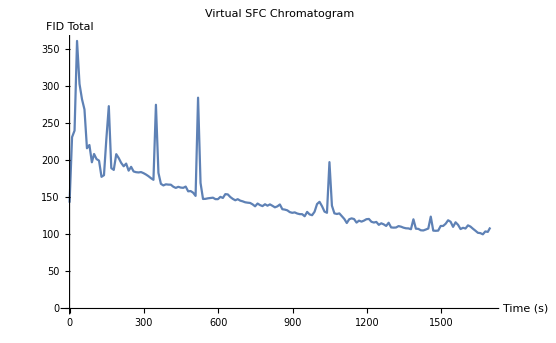

It looks the way I remember it, and I think it will prove useful. The sloping baseline is not caused by anything in the SFC: remember that this is a virtual chromatogram. It is caused by contaminants eluting from the GC column, which would also explain the corrugations on the base plane of the 2D chromatogram.

### Parameter files

Investigating the code showed that the parameter file is  created when SFC_State = 4. But it is also created for as long as SFC_State = 4. Since SFC_State = 4 is the time during which data is not recorded (to save time while the void volume is eluted), a new file is created for every loop of the program! It is overwritten, so the disk does not fill up, but it also means the creation time for the file is the last file written before the GC runs start. This is not a big problem, but if there is no dead time, no parameter file is created at all. This is not acceptable, and the code will have to be corrected.

## Conclusion

The SFC×GC instrument seems to be running OK if it is not interrupted, and the virtual SFC chromatogram is a useful addition. The parameter files issue has been identified.

## Recommendations

Do more SFC×GC runs, but increase the GC column head pressure.

Change the code so that parameter files are created reliably.

Check if there is load shedding, check the stage, and check the schedule. Do not start a run if it will run over the load shedding schedule boundaries.